# Практикум 4

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр. Ковалевская В.С.
  14 октября 2021

### Виртуальная модель пирамиды

```mathematica
Hanoi[1,{from_,to_,_}]:={{from,to}};
```

```mathematica
ClearAll[Ring];
```

```mathematica
Ring[radius_Integer(*радиус диска в виде цедого числа*),{x_,y_}(*координаты центра нижней грани этого диска*)]:={GrayLevel[0.7],Rectangle[{x-radius,y},{x+radius,y+0.9}](*графический объект в виде прямоугольника, где {x-radius,y} - координаты левой нижней точки, {x+radius,y+0.9} - правой верхней точки *)};
```

```mathematica
Ring[5,{3,1}]
```

{GrayLevel[0.7],Rectangle[{-2,1},{8,1.9}]}

Ring создает графический объект для отображения диска.

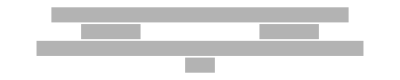

```mathematica
Show[Graphics[{Ring[11,{0,0}],Ring[2,{6,1}],Ring[2,{-6,1}],Ring[10,{0,2}],Ring[1,{0,-1}]}]]
```

```mathematica
Tower[height_Integer,x_Integer,{}]:={GrayLevel[0],Line[{{-1-height+x,0},{x+height+1,0}}],Line[{{x,0},{x,height+1}}]}
```

```mathematica
Tower[height_Integer(*высота башни в виде целого числа*),x_Integer(*координата основания башни в виде целого числа*),{}(*готовим стержень без дисков*)]:={GrayLevel[0],Line[{{-1-height+x,0},{x+height+1,0}}],Line[{{x,0},{x,height+1}}]};
```

```mathematica
Tower[3,2,{}]
```

{GrayLevel[0],Line[{{-2,0},{6,0}}],Line[{{2,0},{2,4}}]}

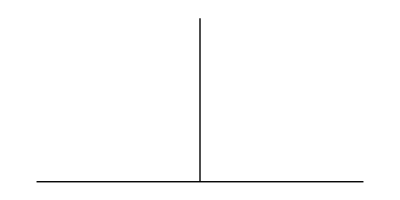

```mathematica
Graphics[Tower[3,2,{}]]
```

```mathematica
Tower[height_Integer,x_Integer,{disk___Integer}]:=Join[Tower[height,x,{}],MapIndexed[Ring[#1,{x,Length@{disk}-#2[[1]]}(*готовим диски на стержне, у каждого своя координата *)]&,{disk}(*список дисков*)]]
```

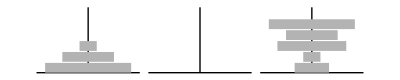

```mathematica
Show[Graphics[{Tower[5,-13,{1,3,5}],Tower[5,0,{}],Tower[5,13,{5,3,4,1,2}]}]]
```

```mathematica
ClearAll[Towers];
Towers[height_Integer,{{A___Integer},{B___Integer},{C___Integer}}(*список трех списков, эл-ты каждого из трех списков - радиусы дисков, находящихся на соответствующем стержне*),opts___]:=Show[Graphics[Join[Tower[height,-2 height-1,{A}],Tower[height,0,{B}],Tower[height,2 height+1,{C}]],PlotRange->All,AspectRatio->Automatic,Axes->False]]
```

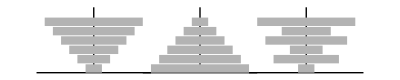

```mathematica
Towers[6,{{6,5,4,3,2,1},{1,2,3,4,5,6},{6,3,5,2,4,1}}]
```

```mathematica
Join[Tower[height,-2 height-1,{A}],Tower[height,0,{B}],Tower[height,2 height+1,{C}]]
```

Tower[height,-1-2 height,{A},height,0,{B},height,1+2 height,{C}]

```mathematica
MapThread
```

### Функция Hanoi

```mathematica
ClearAll[Hanoi];
Hanoi[1,{from_,to_,_}]:={{from,to}};
Hanoi[n_Integer?Positive(*кол-во дисков*),{from_,to_,aux_}(*имена стержней - с какого(from) на какой(to)  посредством какого*)]:=Join[Hanoi[n-1,{from,aux,to}],{{from,to}},Hanoi[n-1,{aux,to,from}]]
```

```mathematica
ClearAll[Hanoi];
Hanoi[1,{from_,to_,_}]:={{from,to}};
Hanoi[n_Integer?Positive,{from_,to_,aux_}]:=Join[Hanoi[n-1,{from,aux,to}],{{from,to}},Hanoi[n-1,{aux,to,from}]]
```

```mathematica
Hanoi[1,{A,B,С}]
```

{{A,B}}

```mathematica
Hanoi[2,{A,B,С}]
```

{{A,С},{A,B},{С,B}}

```mathematica
{{A,С},{A,B},{С,B}}(*писок пар имен стержней - с какого на какой*)
```

{{A,С},{A,B},{С,B}}

```mathematica
Hanoi[3,{A,B,С}]
```

{{A,B},{A,С},{B,С},{A,B},{С,A},{С,B},{A,B}}

```mathematica
Hanoi[10,{A,B,С}]//Short
```

{{A,С},{A,B},{С,B},{A,С},{B,A},{B,С},{A,С},{A,B},{С,B},{С,A},{B,A},«1001»,{B,A},{B,С},{A,С},{A,B},{С,B},{С,A},{B,A},{С,B},{A,С},{A,B},{С,B}}

Модифицируем ф-цию так, чтобы пользователь мог иметь наглядную инструкцию для реализации этого процесса.

```mathematica
ClearAll[Hanoi];
Hanoi[1,Towers_List:{1,2,3},Action_:List]:={Action@@Towers[[{1,2}]]};
Hanoi[n_Integer?Positive,Towers_List:{1,2,3},Action_:List]:=Join[Hanoi[n-1,Towers[[{1,3,2}]],Action],{Action@@Towers[[{1,2}]]},Hanoi[n-1,Towers[[{3,2,1}]],Action]];
```

```mathematica
Hanoi[3]
```

{{1,2},{1,3},{2,3},{1,2},{3,1},{3,2},{1,2}}

```mathematica
Hanoi[4,{A,B,С},Rule]
```

{A→С,A→B,С→B,A→С,B→A,B→С,A→С,A→B,С→B,С→A,B→A,С→B,A→С,A→B,С→B}

```mathematica
Hanoi[2,Range[3],Print[StringForm["Диск с ``го стержня переложить на ``й стержень.",#1,#2]]&]
```

Диск с 1го стержня переложить на 3й стержень.

Диск с 1го стержня переложить на 2й стержень.

Диск с 3го стержня переложить на 2й стержень.

### Главная функция перекладывания дисков

```mathematica
ClearAll[HanoiTower];
HanoiTower[n_Integer?Positive]:=Module[{tower= {Range[n],{},{}}},Join[{Towers[n,tower]},Hanoi[n,{1,2,3},(PrependTo(*как положить диск, т.е. tower[[#2]] - куда положить, First@tower[[#1]]] - что положить*)[tower[[#2]],First@tower[[#1]]];tower[[#1]]=Rest@tower[[#1]](*убрать диск*);Towers[n,tower])&]]]
```

```mathematica
ClearAll[HanoiTower];
HanoiTower[n_Integer?Positive]:=Module[{tower= {Range[n],{},{}}},Join[{Towers[n,tower]},Hanoi[n,{1,2,3},(PrependTo[tower[[#2]],First@tower[[#1]]];tower[[#1]]=Rest@tower[[#1]];Towers[n,tower])&]]]
```

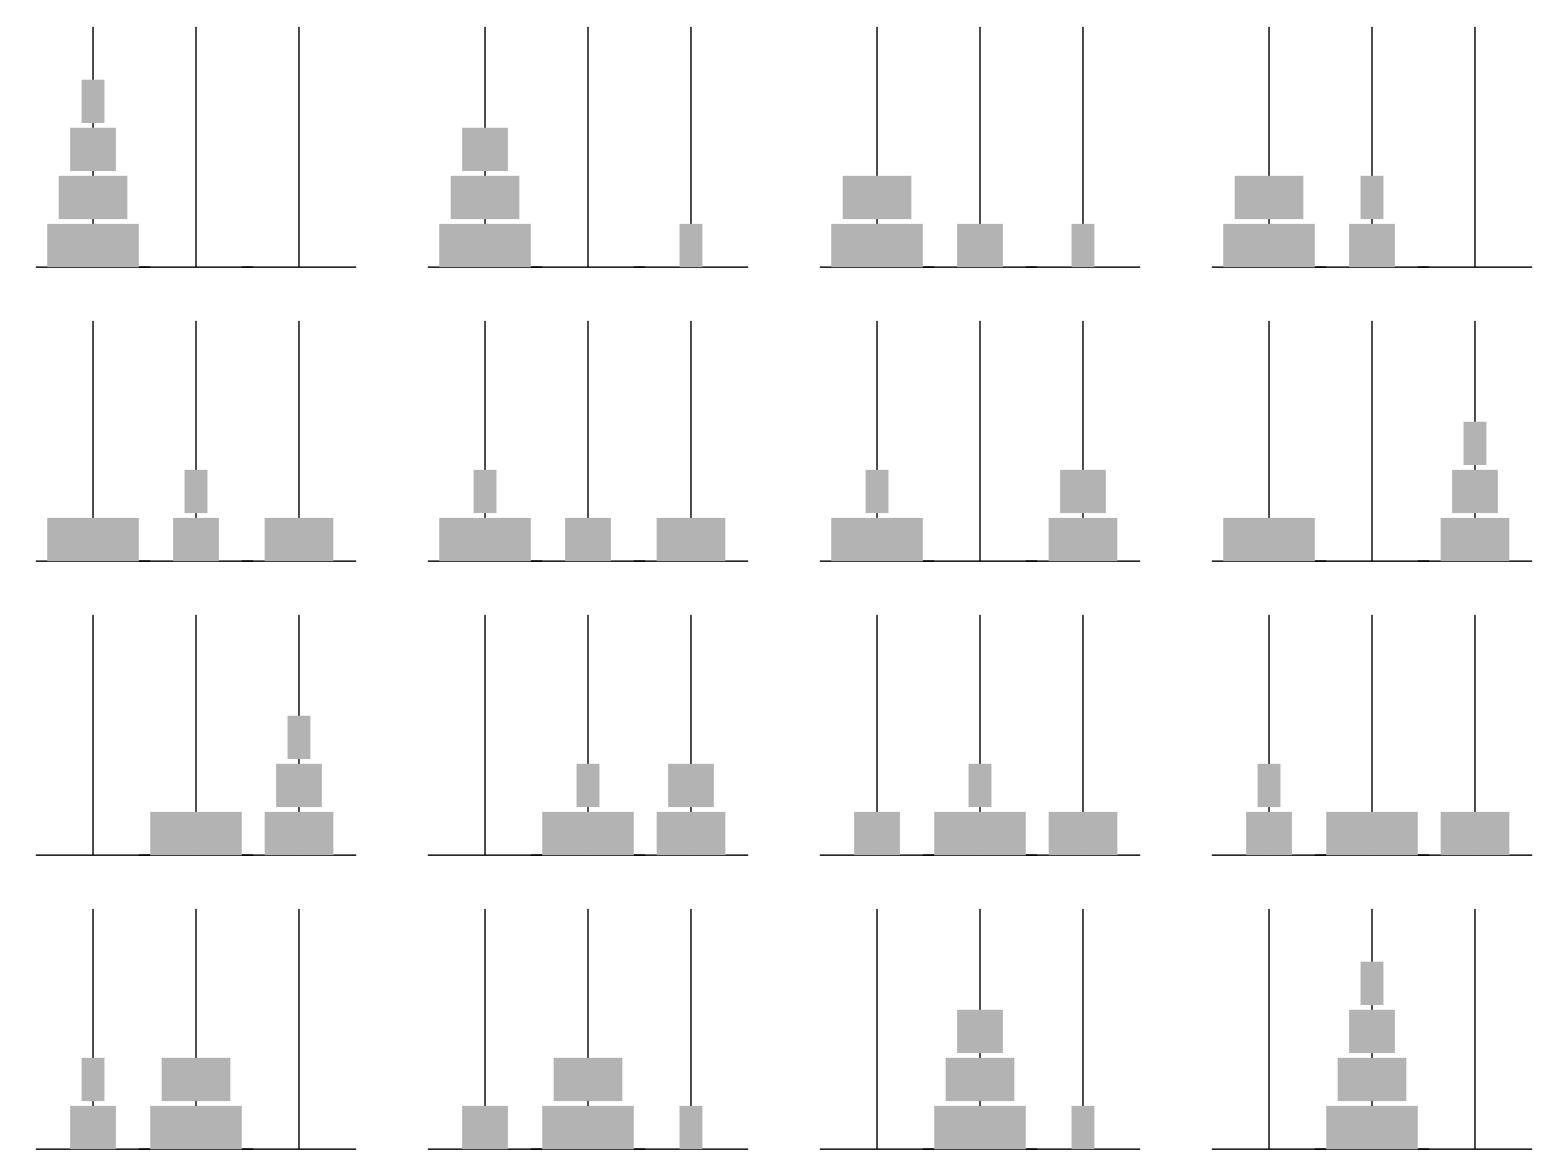

```mathematica
Grid@Partition[HanoiTower[4],4]
```

```mathematica
ListAnimate[Solution=HanoiTower[8],1]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export[ExpandFileName["Hanoi8.FLV"],Solution];
```

### Псевдообъемное изображение

```mathematica
ClearAll[Ring];
Ring[r_Integer,{x_,y_},Δ_:30]:={Table[{GrayLevel[0.75i/Δ],Rectangle[{x+r(i-1)/Δ,y},{x+r i/Δ,y+0.9}],Rectangle[{x-r(i-1)/Δ,y},{x-r i/Δ,y+0.9}]},{i,Δ}]};
```

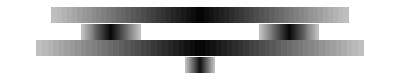

```mathematica
Show[Graphics[{Ring[11,{0,0}],Ring[2,{6,1}],Ring[2,{-6,1}],Ring[10,{0,2}],Ring[1,{0,-1}]}]]
```

```mathematica
ClearAll[f];
{f[-1]==0.8,f'[-0.7]==0 (*производная равна нулю*),f[-0.6]==0.2,f'[0.7]==0,f[0.7]==0.9,f[1]==0.5};
f[t_]=Array(*массив a[1], a[2], a[3]...*)[a,Length@%(*длина списка, который стоит вверху*)].(*скалярное произведение*)t^Range[0,Length@%–1](*1, t, t^2 ...*)
First(*т.к. список одного списка - убираем вложенность*)[Solve[%%(*вычисленный второй с конца*)]]
f[t_]=(*сетом зафиксировали результат*)Together[%%/.%(*возьми последнее вычисленное и подставь предпоследнее вычисленное*)]
```

Range::range: Range specification in Range[0,6 –] does not have appropriate bounds.

{a[1],a[2],a[3],a[4],a[5],a[6]}.t^Range[0,6 –]

{{a[1],a[2],a[3],a[4],a[5],a[6]}.1→0.5,{a[1],a[2],a[3],a[4],a[5],a[6]}.(-1)^Range[0,6 –]→0.8,{a[1],a[2],a[3],a[4],a[5],a[6]}.(-0.6)^Range[0,6 –]→0.2,{a[1],a[2],a[3],a[4],a[5],a[6]}.0.7^Range[0,6 –]→0.9,{a[1],a[2],a[3],a[4],a[5],a[6]}.((-0.7)^(-1+Range[0,6 –]) Range[0,6 –])→-{0,0,0,0,0,0}.(-0.7)^Range[0,6 –],{a[1],a[2],a[3],a[4],a[5],a[6]}.(0.7^(-1+Range[0,6 –]) Range[0,6 –])→-{0,0,0,0,0,0}.0.7^Range[0,6 –]}

{a[1],a[2],a[3],a[4],a[5],a[6]}.t^Range[0,6 –]

```mathematica
ClearAll[f];
{f[-1]==0.8,f'[-0.7]==0, f[-0.6]==0.2, f'[0.7]==0,f[0.7]==0.9, f[1]==0.5};
f[t_]=Array[a,Length@%].t^Range[0,Length@%-1]
First[Solve[%%]]
f[t_]=Together[%%/.%]
```

a[1]+t a[2]+t^2 a[3]+t^3 a[4]+t^4 a[5]+t^5 a[6]

{a[1]→0.641005,a[2]→0.415815,a[3]→-0.440734,a[4]→0.977536,a[5]→0.449729,a[6]→-1.54335}

0.641005+0.415815 t-0.440734 t^2+0.977536 t^3+0.449729 t^4-1.54335 t^5

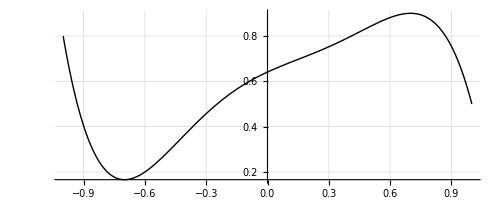

```mathematica
Plot[f[t],{t,-1,1}, AspectRatio->Automatic,GridLines->Automatic,PlotStyle->Directive[Black,Thick]]
```

```mathematica
ClearAll[Ring];
Ring[radius_Integer,{x_,y_},dr_:1/10]:=Table[{GrayLevel@f[r/radius],Rectangle[{x+r-dr,y},{x+r,y+0.9}]},{r,-radius+dr,radius,dr}];
```

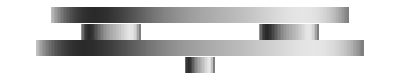

```mathematica
Show[Graphics[{Ring[11,{0,0}],Ring[2,{6,1}],Ring[2,{-6,1}],Ring[10,{0,2}],Ring[10,{0,2}],Ring[1,{0,-1}]}]]
```

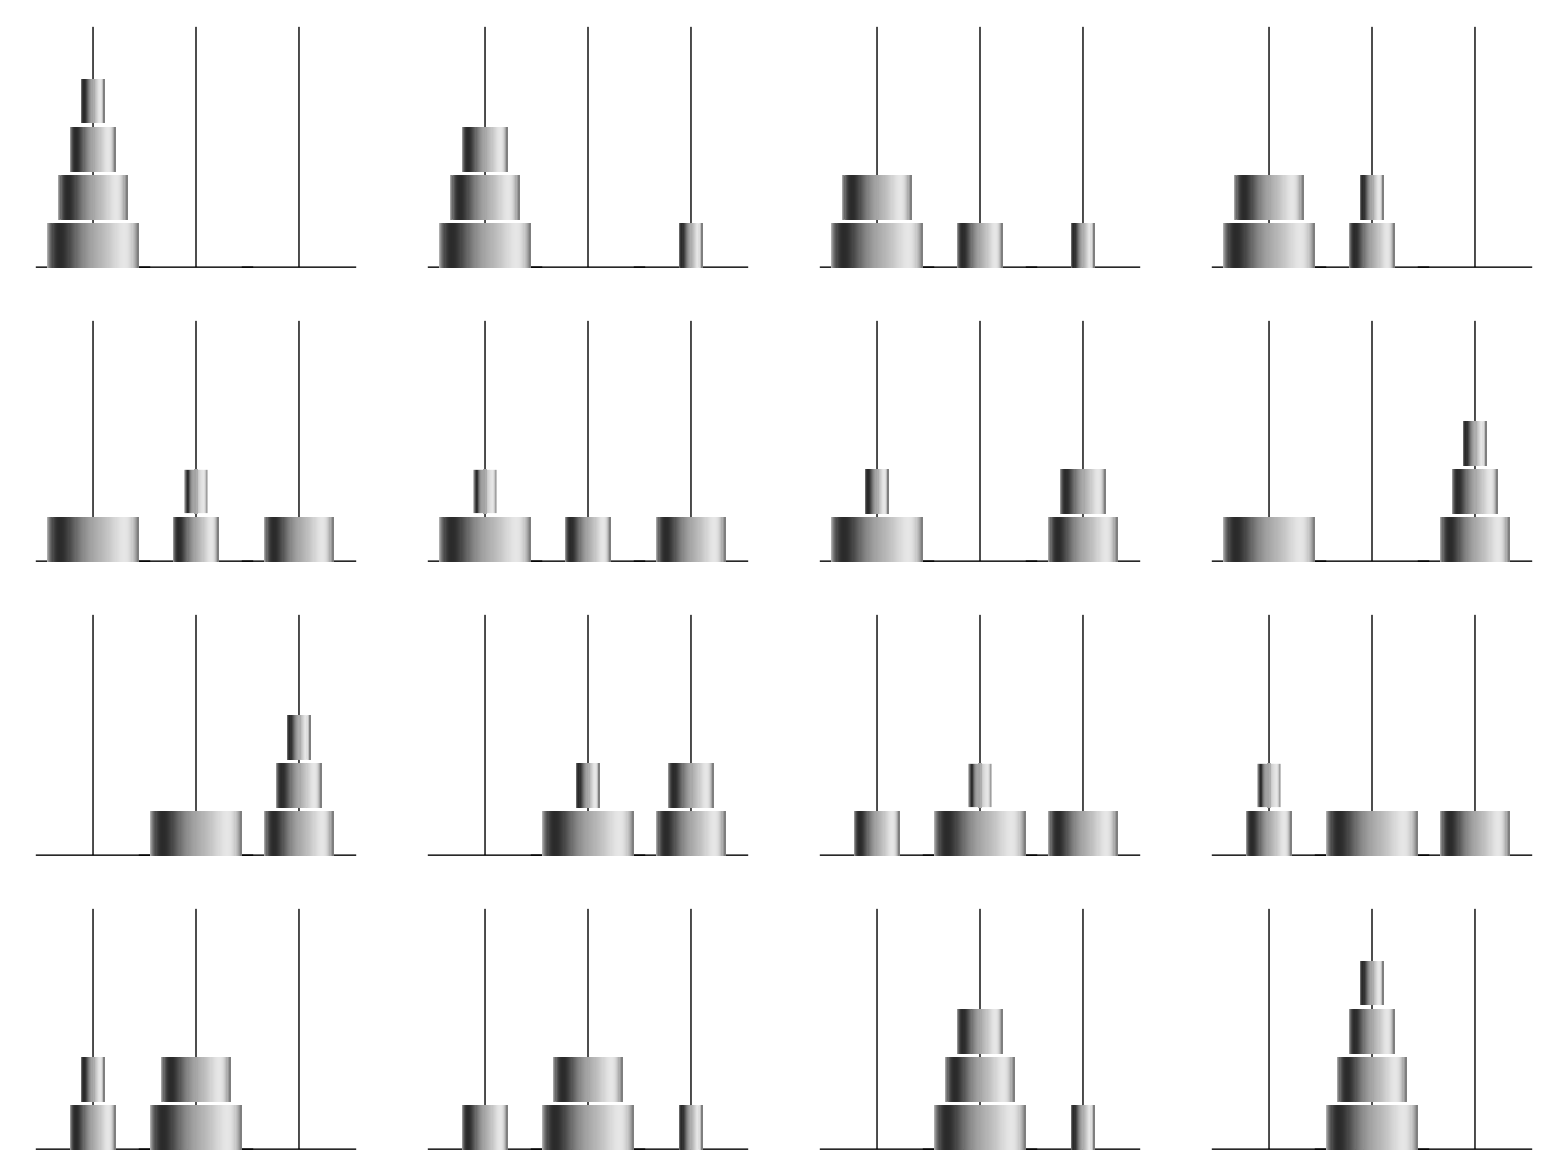

```mathematica
Grid@Partition[Solution=HanoiTower[4],4]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export[ExpandFileName["Hanoi4.GIF"],Solution,"Loop"->True,"AnimationDisplayTime"->1,"Transparency"->White,"Background"->White,"Disposal"->Background];
```

## Кривая, управляемая заданными точками

```mathematica
ClearAll[Bezier];
Bezier[P:{__}][t_]:=Bezier[P][1-t,t];
Bezier[{P_}][mLeft_,mRight_]:=P;
Bezier[P:{__}][mLeft_,mRight_]:=mLeft Bezier[Most@P][mLeft,mRight]+mRight Bezier[Rest@P][mLeft,mRight];
Do[Print[n,": ",Collect[Bezier[Subscript["P", #]&/@Range[0,n]][Subscript[μ, 0],Subscript[μ, 1]],{Subscript[μ, 0],Subscript[μ, 1]}]],{n,0,6}]
```

0: P_0

1: P_0 μ_0+P_1 μ_1

2: P_0 μ_0^2+2 P_1 μ_0 μ_1+P_2 μ_1^2

3: P_0 μ_0^3+3 P_1 μ_0^2 μ_1+3 P_2 μ_0 μ_1^2+P_3 μ_1^3

4: P_0 μ_0^4+4 P_1 μ_0^3 μ_1+6 P_2 μ_0^2 μ_1^2+4 P_3 μ_0 μ_1^3+P_4 μ_1^4

5: P_0 μ_0^5+5 P_1 μ_0^4 μ_1+10 P_2 μ_0^3 μ_1^2+10 P_3 μ_0^2 μ_1^3+5 P_4 μ_0 μ_1^4+P_5 μ_1^5

6: P_0 μ_0^6+6 P_1 μ_0^5 μ_1+15 P_2 μ_0^4 μ_1^2+20 P_3 μ_0^3 μ_1^3+15 P_4 μ_0^2 μ_1^4+6 P_5 μ_0 μ_1^5+P_6 μ_1^6

Формула для 2-х точечной кривой: P = (1-t) P1 + t P2
Для 3-х точек: P = (1-t)^2P1 + 2(1-t) t P2 + t^2 P3
Для 4-х точек: P = (1-t)^3P1 + 3(1-t)^2 t  P2 + 3 (1-t) t^2 P3 + t^3 P4
B [ P_0, P_1, ...  P_(n-1),P_n,] (t) = Σ_(i=0)^n  P_i (C^i)_n t^i (1 (-t))^(n-i)

```mathematica
ClearAll[Bezier];
Bezier[P:{__}][t_]:=Module[{n=Length[P]-1},Sum[P[[i+1]] Binomial[n,i] t^i (1-t)^(n-i),{i,0,n}]];
```

```mathematica
ClearAll[PlotCurve];
SetAttribute[PlotCurve,HoldFirst];
PlotCurve[Parametrization_]:=PlotCurve[Parametrization,{t,0,1}];
PlotCurve[Parametrization_,{t_Symbol}]:=PlotCurve[Parametrization,{t,0,1}];
PlotCurve[Parametrization_,{t_Symbol,t0_,t1_}]:=PlotCurve[Parametrization,{t,t0,t1,.01(t1-t0)}];
PlotCurve[Parametrization_,{t_Symbol,t0_,t1_,dt_}]:=Line@Table[Parametrization,{t,t0,t1,dt}];
```

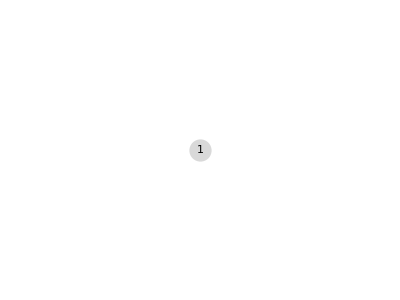

```mathematica
Block[{L=20,H=5,P,B}, 
P=({{0}, {0}}{{0}, {2H}}{{0}, {H}}{{.5L}, {0}}{{L}, {H}}{{L}, {2H}}{{L}, {0}})//Transpose;
B=Collect[Bezier[P][t],t];
Show[Graphics[{{Dotted,Line@P},PlotCurve[B],AbsolutePointSize[16],MapIndexed[{{LightGray,Point @ #},Text[#2[[1]],#]}&,P]}]]]
```

## Траектория движения диска

```mathematica
Moving[H_(*высота башен*),{xFrom_(*горизонтальная координата исходной башни*),yFrom_(*на какой высоте диск лежал на исходной башне*)},{xTo_(*горизонтальная координата конечной башни*),yTo_(*на какой высоте диск будет лежать на конечной башне*)}]:=Function[t,Evaluate@Expand@Bezier[{{xFrom,yFrom},{xFrom, 2H},{xFrom, H}, {0.5 (xFrom+xTo), 0},{xTo,H},{xTo,2H},{xTo,yTo}}]@t]
```

```mathematica
Moving[H_,{xFrom_,yFrom_},{xTo_,yTo_}]:=Function[t,Evaluate@Expand@Bezier[{{xFrom,yFrom},{xFrom, 2H},{xFrom, H}, {0.5 (xFrom+xTo), 0},{xTo,H},{xTo,2H},{xTo,yTo}}]@t]
```

{-11.+220 t^3-330 t^4+132 t^5,4+48 t-210 t^2+280 t^3-30 t^4-132 t^5+40 t^6}

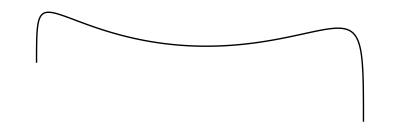

```mathematica
ClearAll[P];
P[t_]=Moving[6,{-11,4},{11,0}][t]
Graphics[PlotCurve[P[t]]]
```

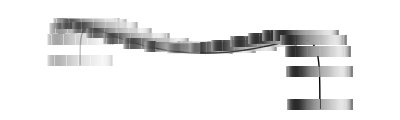

```mathematica
Graphics[{Table[{Opacity[.2+.8 t],
If[t>0,Line@Table[P[t+dt],{dt,-.05,0,.01}]],
Ring[3,P[t]]},{t,0,1,.05}]},PlotRange->{{-15,15},{0,9}}]
```

## Перекладывание дисков

```mathematica
ClearAll[HanoiTower];
HanoiTower[n_Integer?Positive]:=Module[{ring, trace, T, X={-2 n-1,0,2 n+1},
tower={Range[n],{},{}},
PR={4 n{-1,1},{-.5,2 n}}},
Hanoi[n,{1,2,3},(ring=tower[[#1,1]];
Show@Towers[n,tower,PlotRange->PR]; tower[[#1]]=Rest[tower[[#1]]];T=Towers[n, tower,PlotRange->PR]; trace=Moving[n+1,{X[[#1]],Length[tower[[#1]]]},{X[[#2]],Length[tower[[#2]]]}];
Do[Sow@Show[T,Graphics[Ring[ring,trace[t]]],PlotRange->PR],{t,0,1,.05}];
PrependTo[tower[[#2]],ring])&]];
```

```mathematica
ListAnimate[Movies=Reap[HanoiTower[5]][[2,1]]]
```